```mathematica
ClearAll["Global`*"]
```

```mathematica
Adata={76,82,96,100,116,128,130,150};
DeltaP={1.363,1.289,0.398,2.099,0.636,1.965,1.678,1.181};
SQRTA={1.376,1.325,1.224,1.2,1.114,1.061,1.052,0.979};
(*1/2sqrtA*)
```

## Te rog sa plotezi cu simboluri diferite pe acelasi grafic, DELTAP (adica \Delta_p ca functia de A si 12PESQRTA (adica 12/\sqrt{A}) ca functie de A

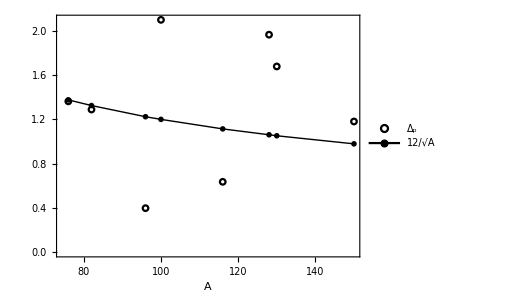

```mathematica
plot=ListPlot[{Table[{Adata[[i]],DeltaP[[i]]},{i,1,Length[Adata]}],Table[{Adata[[i]],SQRTA[[i]]},{i,1,Length[Adata]}]},Joined->{False, True},Frame->True,Axes->False,AspectRatio->0.8,FrameStyle->Directive[Black,Thick],LabelStyle->{22,Bold,Black,FontFamily->"Times"},FrameLabel->{"A"},PlotRange->All,PlotStyle->{{Black},{Black,Thick}},PlotMarkers->{{Graphics[{Circle[]}],1/18},{Graphics[{Disk[]}],1/20}},PlotLegends->Placed[{"Δ_p","12/√A"},{0.8,0.18}],ImageSize->380];
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/Delta-plots/figure-1/figure-1.pdf",Show[plot],ImageResolution->1200];
Show[plot]
```



PlotMarkers→{{-Graphics-,1/4},{-Graphics-,1/8}}

```mathematica
PlotMarkers->{{Graphics[{Disk[]}],1/4},{Graphics[{Rectangle[]}],1/8}}
```

```mathematica
PlotMarkers->{{"•",Scaled[0.08]},{"▽",Scaled[0.08]}}
```

PlotMarkers→{{•,Scaled[0.08]},{▽,Scaled[0.08]}}